# Gran Test Error

Se analizará de nuevo el error. Esta vez, se implementó el algoritmo MH correctamente

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"MaTeX`"
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/gran_test_error"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/gran_test_error

```mathematica
betas = {10, 50, 100, 250, 500, 750, 1000};
deltas = {0.001, 0.005, 0.01, 0.03, 0.05, 0.07, 0.1};
ene = 20000;
rzs = {0, 0.5, 0.8};
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs;
```

## Objetivo r_z = 0

### p = 0.3

```mathematica
errorDataR0Pp3 = {
	errorsR0Pp3β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas	
};
```

```mathematica
Clear[errorsR0Pp3β1, errorsR0Pp3β2, errorsR0Pp3β3, errorsR0Pp3β4, errorsR0Pp3β5, errorsR0Pp3β6, errorsR0Pp3β7]
```

```mathematica
errorVSβDataR0Pp3 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataR0Pp3, betas}]//Transpose;
```

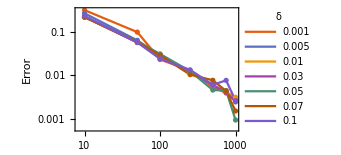
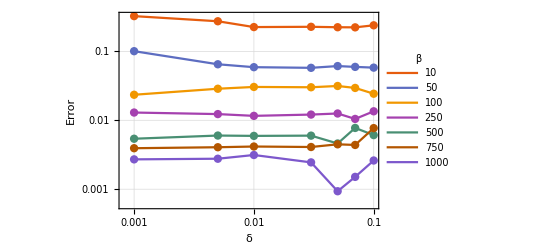

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataR0Pp3, errorDataR0Pp3}, {deltas, betas}, {δ, β}, {β, δ}}]
```

```mathematica
samplesδp001 = Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0_p=0.3.wl"][[2]]& /@ betas;
```

```mathematica
distsδp001 = distsToTarget[#[[1]], targets[[1]], 0.3]& /@ samplesδp001;
```

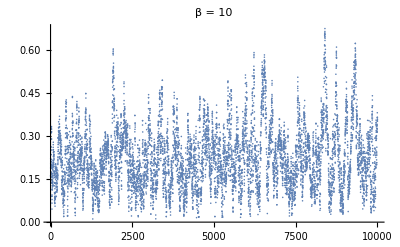
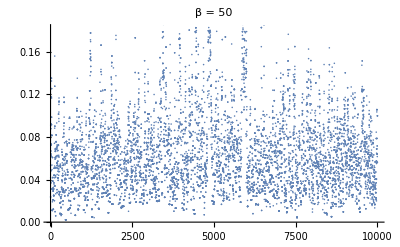
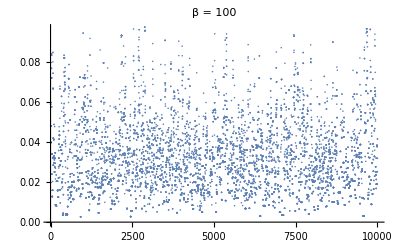
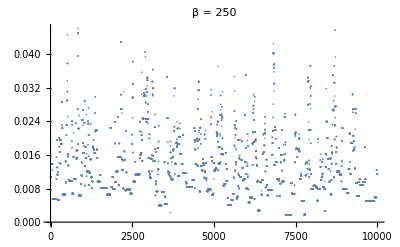
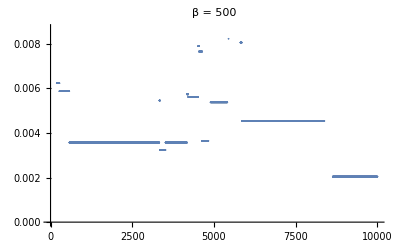
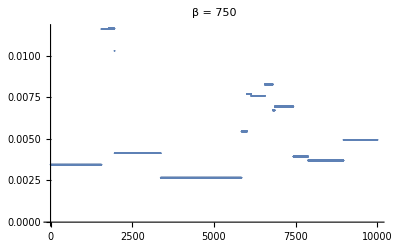
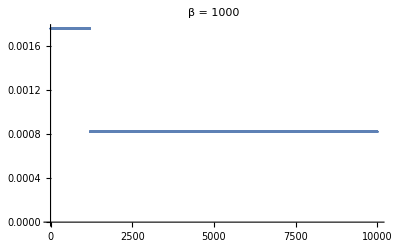

```mathematica
MapThread[ListPlot[#1[[10000;;]], PlotLabel->"β = "<>ToString[#2]]&, {distsδp001, betas}]
```

### p = 0.5

```mathematica
errorDataR0Pp5 = {
	errorsR0Pp5β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas	
};
```

```mathematica
Clear[errorsR0Pp5β1, errorsR0Pp5β2, errorsR0Pp5β3, errorsR0Pp5β4, errorsR0Pp5β5, errorsR0Pp5β6, errorsR0Pp5β7]
```

```mathematica
errorVSβDataR0Pp5 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataR0Pp5, betas}]//Transpose;
```

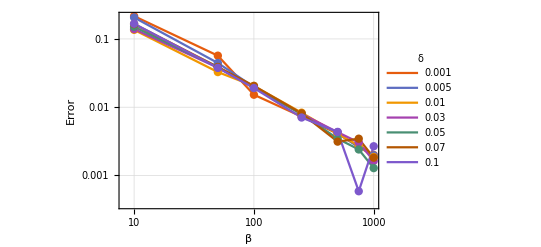
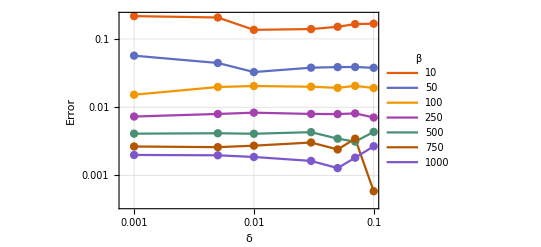

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataR0Pp5, errorDataR0Pp5}, {deltas, betas}, {δ, β}, {β, δ}}]
```

### p = 0.8

```mathematica
errorDataR0Pp8 = {
	errorsR0Pp8β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas	
};
```

```mathematica
Clear[errorsR0Pp8β1, errorsR0Pp8β2, errorsR0Pp8β3, errorsR0Pp8β4, errorsR0Pp8β5, errorsR0Pp8β6, errorsR0Pp8β7]
```

```mathematica
errorVSβDataR0Pp8 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataR0Pp8, betas}]//Transpose;
```

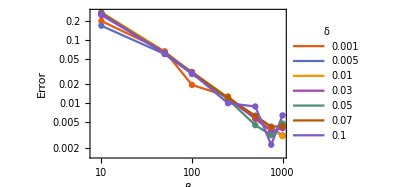
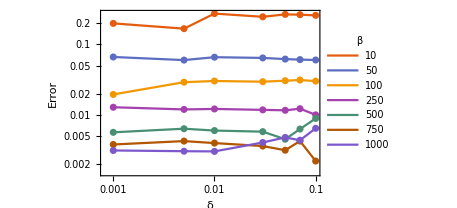

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataR0Pp8, errorDataR0Pp8}, {deltas, betas}, {δ, β}, {β, δ}}]
```

## Objetivo r_z= 0.5

### p = 0.3

```mathematica
errorDataRp5Pp3 = {
	errorsRp5Pp3β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas,
	errorsRp5Pp3β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas,
	errorsRp5Pp3β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas,
	errorsRp5Pp3β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas,
	errorsRp5Pp3β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas,
	errorsRp5Pp3β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas,
	errorsRp5Pp3β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp5Pp3β1, errorsRp5Pp3β2, errorsRp5Pp3β3, errorsRp5Pp3β4, errorsRp5Pp3β5, errorsRp5Pp3β6, errorsRp5Pp3β7]
```

```mathematica
errorVSβDataRp5Pp3 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp5Pp3, betas}]//Transpose;
```

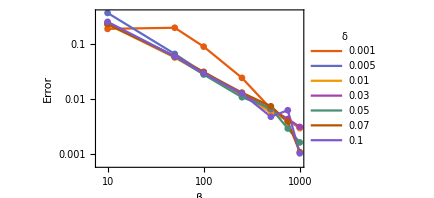
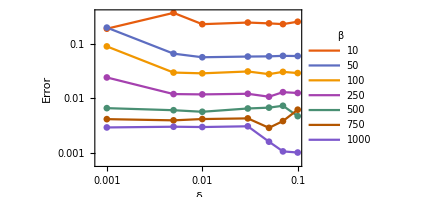

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp5Pp3, errorDataRp5Pp3}, {deltas, betas}, {δ, β}, {β, δ}}]
```

```mathematica
samplesδp001 = Get["MHsample_N=20000_delta=0.001_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ betas;
```

```mathematica
distsδp001 = distsToTarget[#[[1]], targets[[2]], 0.3][[10000;;]]& /@ samplesδp001;
```

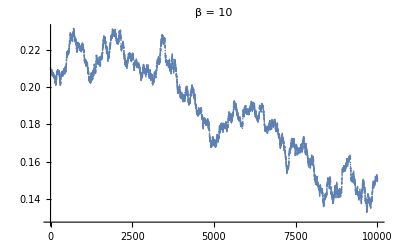
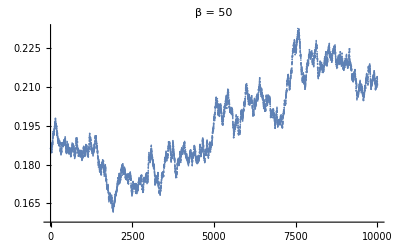
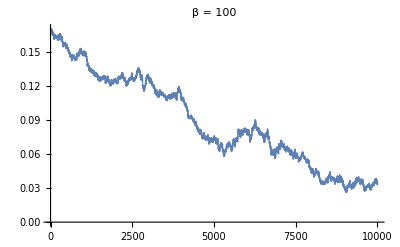
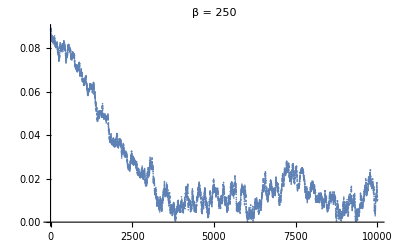
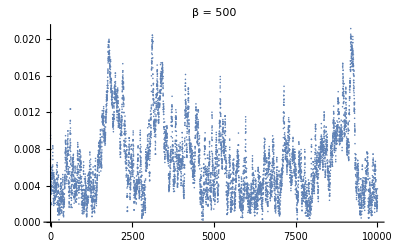
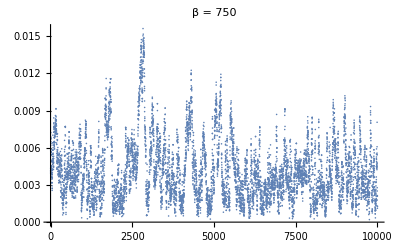
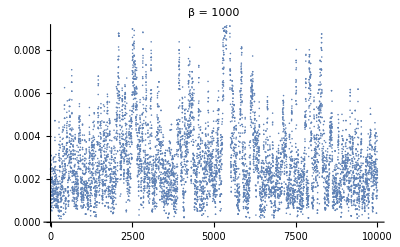

```mathematica
MapThread[ListPlot[#1, PlotLabel->"β = "<>ToString[#2]]&, {distsδp001, betas}]
```

### p = 0.5

```mathematica
errorDataRp5Pp5 = {
	errorsRp5Pp5β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas,
	errorsRp5Pp5β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas,
	errorsRp5Pp5β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas,
	errorsRp5Pp5β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas,
	errorsRp5Pp5β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas,
	errorsRp5Pp5β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas,
	errorsRp5Pp5β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp5Pp5β1, errorsRp5Pp5β2, errorsRp5Pp5β3, errorsRp5Pp5β4, errorsRp5Pp5β5, errorsRp5Pp5β6, errorsRp5Pp5β7]
```

```mathematica
errorVSβDataRp5Pp5 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp5Pp5, betas}]//Transpose;
```

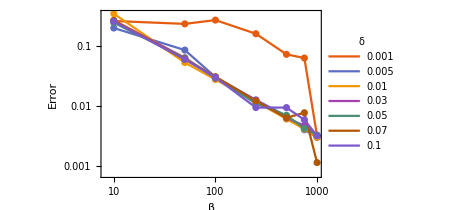
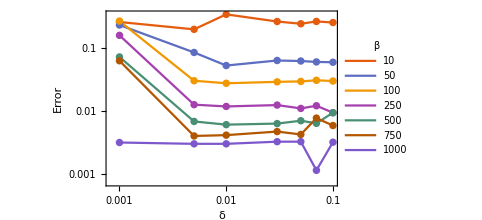

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp5Pp5, errorDataRp5Pp5}, {deltas, betas}, {δ, β}, {β, δ}}]
```

```mathematica
prueba = Get["MHsample_N=20000_delta=0.001_beta=750_rz=0.5_p=0.5.wl"][[2]];
prueba2 = Get["MHsample_N=20000_delta=0.001_beta=1000_rz=0.5_p=0.5.wl"][[2]];
prueba3 = Get["MHsample_N=20000_delta=0.001_beta=50_rz=0.5_p=0.5.wl"][[2]];
```

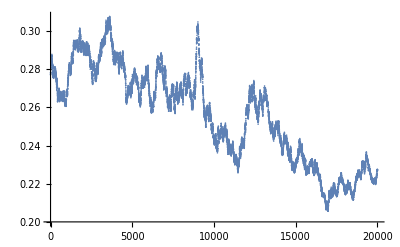
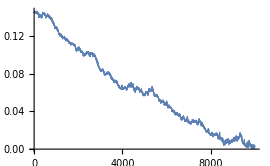
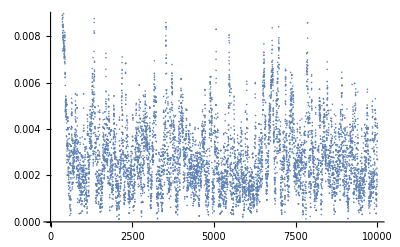

```mathematica
{ListPlot[distsToTarget[prueba3[[1]], targets[[2]], 0.5]], ListPlot[distsToTarget[prueba[[1]][[10000;;]], targets[[2]], 0.5]], ListPlot[distsToTarget[prueba2[[1]][[10000;;]], targets[[2]], 0.5]]}
```

### p = 0.8

```mathematica
errorDataRp5Pp8 = {
	errorsRp5Pp8β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp5Pp8β1, errorsRp5Pp8β2, errorsRp5Pp8β3, errorsRp5Pp8β4, errorsRp5Pp8β5, errorsRp5Pp8β6, errorsRp5Pp8β7]
```

```mathematica
errorVSβDataRp5Pp8 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp5Pp8, betas}]//Transpose;
```

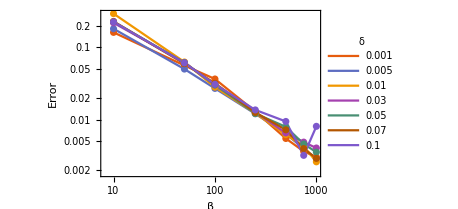
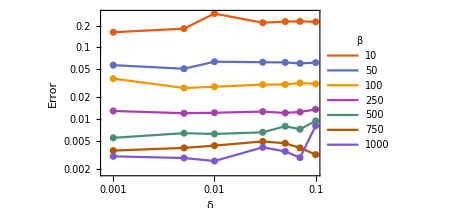

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp5Pp8, errorDataRp5Pp8}, {deltas, betas}, {δ, β}, {β, δ}}]
```

## Objetivo r_z = 0.8

### p = 0.3

```mathematica
errorDataRp8Pp3 = {
	errorsRp8Pp3β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas,
	errorsRp8Pp3β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas,
	errorsRp8Pp3β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas,
	errorsRp8Pp3β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas,
	errorsRp8Pp3β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas,
	errorsRp8Pp3β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas,
	errorsRp8Pp3β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp8Pp3β1, errorsRp8Pp3β2, errorsRp8Pp3β3, errorsRp8Pp3β4, errorsRp8Pp3β5, errorsRp8Pp3β6, errorsRp8Pp3β7]
```

```mathematica
errorVSβDataRp8Pp3 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp8Pp3, betas}]//Transpose;
```

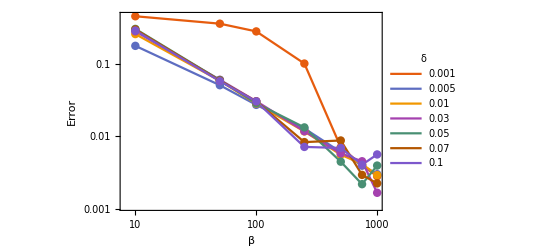
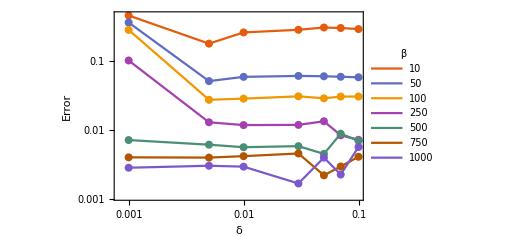

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp8Pp3, errorDataRp8Pp3}, {deltas, betas}, {δ, β}, {β, δ}}]
```

```mathematica
samplesδp001 = Get["MHsample_N=20000_delta=0.001_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2]]& /@ betas;
```

```mathematica
distsδp001 = distsToTarget[#[[1]], targets[[3]], 0.3]& /@ samplesδp001;
```

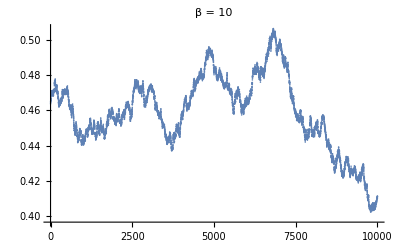
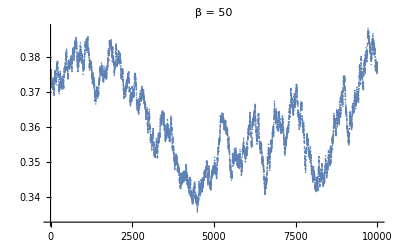
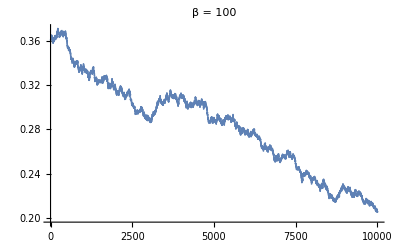
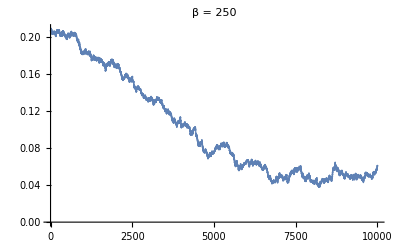
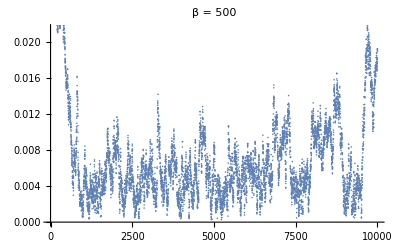
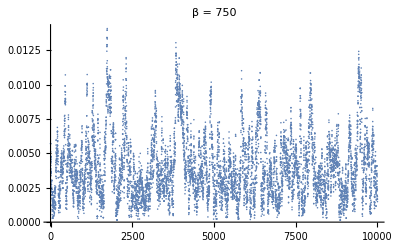
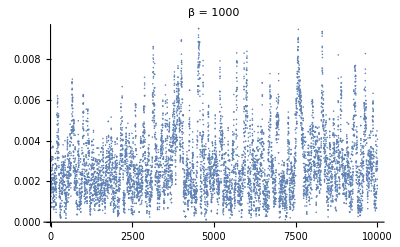

```mathematica
MapThread[ListPlot[#1[[10000;;]], PlotLabel->"β = "<>ToString[#2]]&, {distsδp001, betas}]
```

### p = 0.5

```mathematica
errorDataRp8Pp5 = {
	errorsRp8Pp5β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas,
	errorsRp8Pp5β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas,
	errorsRp8Pp5β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas,
	errorsRp8Pp5β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas,
	errorsRp8Pp5β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas,
	errorsRp8Pp5β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas,
	errorsRp8Pp5β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp8Pp5β1, errorsRp8Pp5β2, errorsRp8Pp5β3, errorsRp8Pp5β4, errorsRp8Pp5β5, errorsRp8Pp5β6, errorsRp8Pp5β7]
```

```mathematica
errorVSβDataRp8Pp5 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp8Pp5, betas}]//Transpose;
```

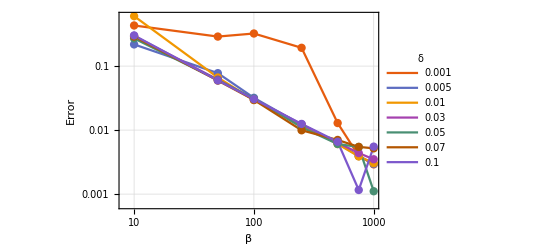
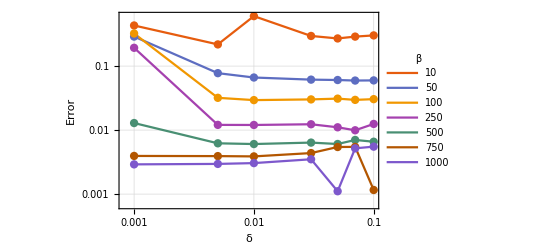

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp8Pp5, errorDataRp8Pp5}, {deltas, betas}, {δ, β}, {β, δ}}]
```

### p = 0.8

```mathematica
errorDataRp8Pp8 = {
	errorsRp8Pp8β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas,
	errorsRp8Pp8β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas,
	errorsRp8Pp8β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas,
	errorsRp8Pp8β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas,
	errorsRp8Pp8β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas,
	errorsRp8Pp8β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas,
	errorsRp8Pp8β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp8Pp8β1, errorsRp8Pp8β2, errorsRp8Pp8β3, errorsRp8Pp8β4, errorsRp8Pp8β5, errorsRp8Pp8β6, errorsRp8Pp8β7]
```

```mathematica
errorVSβDataRp8Pp8 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp8Pp8, betas}]//Transpose;
```

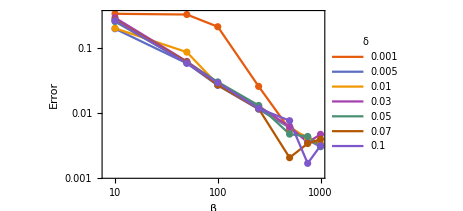
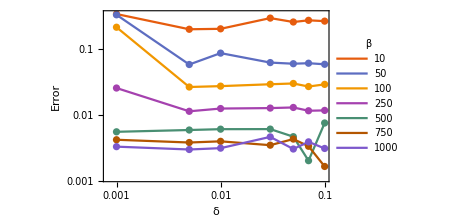

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp8Pp8, errorDataRp8Pp8}, {deltas, betas}, {δ, β}, {β, δ}}]
```

```mathematica
pr = Get["MHsample_N=20000_delta=0.001_beta=100_rz=0.8_p=0.8.wl"][[2]];
```

```mathematica
pr[[2]]//N
```

0.9722

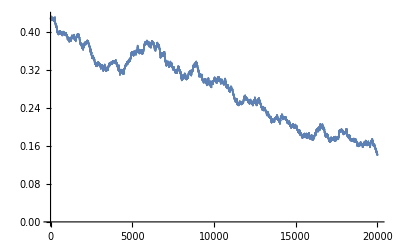

```mathematica
ListPlot[distsToTarget[pr[[1]], targets[[3]], 0.8]]
```

## Corriendo de nuevo para δ = 0.001